## Definitions

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
UninstallJava[];
Ψ=({{ψ1}, {ψ2}, {ψ3}, {ψ4}});
ua=({{u1}, {u2}, {u3}, {u4}});
G0=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}});
Ym=({{y1[t]}, {y2[t]}, {y3[t]}, {y4[t]}});
Ymx=({{y1[x]}, {y2[x]}, {y3[x]}, {y4[x]}});
Ym2=({{y1[x,t]}, {y2[x,t]}, {y3[x,t]}, {y4[x,t]}});
G1=({{0, 0, 0, 1}, {0, 0, 1, 0}, {0, -1, 0, 0}, {-1, 0, 0, 0}});
G2=({{0, 0, 0, -I}, {0, 0, I, 0}, {0, I, 0, 0}, {-I, 0, 0, 0}});
G3=({{0, 0, 1, 0}, {0, 0, 0, -1}, {-1, 0, 0, 0}, {0, 1, 0, 0}});

G5=({{0, 0, 1, 0}, {0, 0, 0, 1}, {1, 0, 0, 0}, {0, 1, 0, 0}});



G1b=({{0, 1, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, -1}, {0, 0, -1, 0}});
G2b=({{0, -I, 0, 0}, {I, 0, 0, 0}, {0, 0, 0, I}, {0, 0, -I, 0}});
G3b=({{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, 1}});

G1c=({{0, 0, 0, -I}, {0, 0, -I, 0}, {0, I, 0, 0}, {I, 0, 0, 0}});
G2c=({{0, 0, 0, -1}, {0, 0, 1, 0}, {0, 1, 0, 0}, {-1, 0, 0, 0}});
G3c=({{0, 0, -I, 0}, {0, 0, 0, I}, {I, 0, 0, 0}, {0, -I, 0, 0}});

A4=I G0.G5;
A5=({{0, 1, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}});
A6=({{0, -I, 0, 0}, {I, 0, 0, 0}, {0, 0, 0, -I}, {0, 0, I, 0}});
A7=({{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, -1}});
A8=G0.G1;
A9=G0.G2;
A10=G0.G3;
A11=-G5.G1;
A12=-G5.G2;
A13=-G5.G1;
A14=I G1;
A15=I G2;
A16=I G3;


gmn=({{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}});
gmn2=({{-1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, 1}});
Σ=({{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, -1}});
I4=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}});
Λ1=({{a, -ba, 0, 0}, {-ba, a, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}});
Λ2=({{c, 0, -d c, 0}, {0, 1, 0, 0}, {-d c, 0, c, 0}, {0, 0, 0, 1}});
R1=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, c, s}, {0, 0, -s, c}});
Λ3=({{e, 0, 0, -f e}, {0, 1, 0, 0}, {0, 0, 1, 0}, {-f e, 0, 0, e}});
M1B=({{a1, b1, c1, d1}, {b1, f1, g1, h1}, {c1, g1, k1, l1}, {d1, h1, l1, p1}});
M1=({{a1, b1, c1, d1}, {b1, a1, g1, h1}, {c1, g1, a1, l1}, {d1, h1, l1, a1}});
M1as=({{a1, b1, c1, d1}, {-b1, a1, g1, h1}, {-c1, -g1, a1, l1}, {-d1, -h1, -l1, a1}});
M1up=({{a1, b1, c1, d1}, {0, a1, g1, h1}, {0, 0, a1, l1}, {0, 0, 0, a1}});
M1dn=({{a1, 0, 0, 0}, {b1, a1, 0, 0}, {c1, g1, a1, 0}, {d1, h1, l1, a1}});

m1=({{a1, b1}, {b1, a1}});

m2=({{a1, b1, c1}, {b1, a1, g1}, {c1, g1, a1}});
M2=({{a2, b2, c2, d2}, {b2, a2, g2, h2}, {c2, g2, a2, l2}, {d2, h2, l2, a2}});
M3=({{a3, b3, c3, d3}, {b3, a3, g3, h3}, {c3, g3, a3, l3}, {d3, h3, l3, a3}});
M4=({{a4, b4, c4, d4}, {b4, a4, g4, h4}, {c4, g4, a4, l4}, {d4, h4, l4, a4}});
M44=({{a4, b4, c4, d4}, {b4, a4, g44, h4}, {c4, g44, a4, l4}, {d4, h4, l4, a4}});
M5=({{a5, b5, c5, d5}, {e5, f5, g5, h5}, {i5, j5, k5, l5}, {m5, n5, o5, p5}});
M11=({{a1, b1, c1, d1}, {b1, a1, g11, h1}, {c1, g11, a1, l1}, {d1, h1, l1, a1}});
K1=({{a1, b1, 0, 0}, {b1, a1, 0, 0}, {0, 0, a1, l1}, {0, 0, l1, a1}});
K1b=({{a1, b1, 0, 0}, {b1, a1, 0, 0}, {0, 0, a1, -b1}, {0, 0, -b1, a1}});
K2=({{a2, b2, c2, 0}, {b2, a2, 0, -c2}, {c2, 0, a2, b2}, {0, -c2, b2, a2}});
K3=({{a3, b3, c3, d3}, {b3, a3, g3, -c3}, {c3, g3, a3, -b3}, {d3, -c3, -b3, a3}});
K3b=({{a3, b3, 0, 0}, {b3, a3, 0, 0}, {0, 0, a3, -b3}, {0, 0, -b3, a3}});
K3b=({{a3, b3, c3, d3}, {b3, a3, -d3, -c3}, {c3, -d3, a3, -b3}, {d3, -c3, -b3, a3}});
K4=({{a4, b4, 0, d4}, {b4, a4, g4, 0}, {0, g4, a4, -b4}, {d4, 0, -b4, a4}});
K4b=({{a4, b4, 0, d4}, {b4, a4, -d4, 0}, {0, -d4, a4, -b4}, {d4, 0, -b4, a4}});
NM=({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
nG0=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}});
nG1=({{0, 0, 1, 0}, {0, 0, 0, -1}, {-1, 0, 0, 0}, {0, 1, 0, 0}});
nG2=({{0, 0, 0, -I}, {0, 0, I, 0}, {0, I, 0, 0}, {-I, 0, 0, 0}});
nG3=({{0, 0, 0, 1}, {0, 0, 1, 0}, {0, -1, 0, 0}, {-1, 0, 0, 0}});
T1=({{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, -1}});
T2=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}});
T3=({{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, 1}});
T4=({{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, -1}});

AL=Sqrt[2]({{0, 0, 0, 0}, {0, 0, 0, 0}, {1, 0, 0, 0}, {0, 1, 0, 0}});(*Levy Leblonds*)
CL =Sqrt[2] ({{0, 0, 1, 0}, {0, 0, 0, 1}, {0, 0, 0, 0}, {0, 0, 0, 0}});
si1=PauliMatrix[1];
si2=PauliMatrix[2];
si3=PauliMatrix[3];
I2=IdentityMatrix[2];
u1a=({{1}, {0}});
u2a=({{0}, {1}});
hh1=({{a, b}, {b, c}});
uh=({{p}, {q}});
n2=({{0}, {0}});
n4=({{0}, {0}, {0}, {0}});
uA=({{u1}, {u2}});
uB=({{u3}, {u4}});

(*Spin matrices Σi*)
Sp1=ArrayFlatten[{{si1,0 IdentityMatrix[2]},{0 IdentityMatrix[2],si1}}];
Sp2=ArrayFlatten[{{si2,0 IdentityMatrix[2]},{0 IdentityMatrix[2],si2}}];
sp3=ArrayFlatten[{{si3,0 IdentityMatrix[2]},{0 IdentityMatrix[2],si3}}];

modsq[x_]:=Conjugate[x] x
com[x_,y_]:=x.y-y.x;
acom[x_,y_]:=x.y+y.x;
herm[x_]:=ConjugateTranspose[x]-x;
sqsum[x_,y_,z_,p_]:=x.x+y.y+z.z+p.p;
comfour[x_,y_,z_,p_]:=(x.y-y.z)+(x.z-z.x)+(x.p-p.z)+(y.z-z.y)+(z.p-p.z);

Mns1=1/Sqrt[2]({{-1, 1}, {-1, 1}});
wrn1=Sqrt[2]({{0, 1}, {0, 0}});
```

```mathematica
$Assumptions={};
```

```mathematica
$Assumptions={e∈Reals ,p0∈Reals ,p1∈Reals ,p2∈Reals ,p3∈Reals,v0∈Reals,z∈Reals,L∈Reals,e>0,m>0,v0>0,L>0,pz>0, pz∈Reals, py∈Reals, e>m, e-v0>m, e>v0+m, hx>0,hx∈Reals,ϵ>0,τ>0,ϵ∈Reals ,τ∈Reals }
```

{e∈ℝ,p0∈ℝ,p1∈ℝ,p2∈ℝ,p3∈ℝ,v0∈ℝ,z∈ℝ,L∈ℝ,e>0,m>0,v0>0,L>0,pz>0,pz∈ℝ,py∈ℝ,e>m,e-v0>m,e>m+v0,hx>0,hx∈ℝ,ϵ>0,τ>0,ϵ∈ℝ,τ∈ℝ}

## antisymmetric matrices

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Adeel\Dropbox\0-Research\NRQM\mathematica\NRQM-Matrx-structure\drafts\so10\A-so10-nilpotent\submission\clean_mathematica

```mathematica
Get["antisymmetric_matrices.m"];
```

```mathematica
Print["Loaded:"];
Print[" Anti Symmetric matrices: ",countAntisymmetricMatrices];
```

Loaded:

Anti Symmetric matrices: 48

```mathematica
me=9.1*10^-31;
cv=3*10^8;
ev=me*cv^2/(1.6*10^-19);
mev=me*cv^2/(1.6*10^-19);
jev=(1.6*10^-19);
vstep=mev;

gv = 0.379;
```

Generate images for all the matrices.

```mathematica
(*Get first symmetric matrix and its c value*)

For[i=1,i<=48,i++,
(M1=getAntisymmetricMatrix[i];
c1=getAntisymmetricCValue[i];

Tcc2=0;
Tcpcp2=0;
Tccp2=0;
Tcpc2=0;

Rbb2=0;
Rbpbp2=0;
Rbbp2=0;
Rbpb2=0;

Print["\nExample matrix:"];
Print[MatrixForm[M1]];
Print["c value: ",c1];

(*Verify properties*)
Print["Nilpotent (M^2 = 0): ",verifyNilpotent[M1]];
Print["Anticommutator constraint: ",verifyAnticommutator[M1]];

 c2= If[c1==4,c1,c1/4*Sqrt[2]];
eta =c2/8*Sqrt[2]  M1;


x1 = (eta + ConjugateTranspose[eta])/Sqrt[2];
x2 =  (eta - ConjugateTranspose[eta])/Sqrt[2];

Eigenvalues[ eta  e+  m ConjugateTranspose[eta] ];
Eigenvalues[ x1  e+  m  x2];

Pz =Eigenvectors[  x1  e+  m  x2];

PzA = Pz/. { 1/e^(1/2) ->(Sqrt[2]Sqrt[m])/pz};

PzB = PzA/. { Sqrt[e] Sqrt[m]->pz/Sqrt[2],- Sqrt[e] Sqrt[m]->-pz/Sqrt[2], Sqrt[e^2 - m^2]->pz, Sqrt[e] ->pz/(Sqrt[2]Sqrt[m])
, 1/e^(1/2) ->(Sqrt[2]Sqrt[m])/pz, 1/Sqrt[e^2 - m^2]->1/pz, √(-e^2+m^2)->I pz};

P={{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,0}};

PzD =PzB.P;

col[v_]:=List/@v;

u1=col[PzD[[3]]];
     u2=col[PzD[[4]]];

u3=col[PzD[[1]]];
     u4=col[PzD[[2]]];

Fu1[ee_,ppz_]:=u1/. {e->ee, pz->ppz};
Fu2[ee_,ppz_]:=u2/. {e->ee, pz->ppz};
Fu3[ee_,ppz_]:=u3/. {e->ee, pz->ppz};
Fu4[ee_,ppz_]:=u4/. {e->ee, pz->ppz};

psiIN = a Fu1[e,p1];
psiR = b Fu1[e,-p1] + bp Fu2[e,-p1];
psiT = c  Fu1[e-v0,p2]+ cp Fu2[e-v0,p2];

Xm=x1;

sol1 = Solve[a Fu1[e,p1]+b Fu1[e,-p1] + bp Fu2[e,-p1]==c  Fu1[e-v0,p2]+ cp Fu2[e-v0,p2],{a,b,c,bp,cp}]//FullSimplify;

sol2 = sol1/.{p1-> Sqrt[e^2-m^2],p2-> Sqrt[(e-v0)^2-m^2]}//FullSimplify;

jin= ConjugateTranspose[psiIN].Xm.psiIN//FullSimplify;

jT = ConjugateTranspose[psiT].Xm.psiT//FullSimplify;

jR= ConjugateTranspose[psiR].Xm.psiR//FullSimplify;

jTjin =jT/jin/.{p1-> Sqrt[e^2-m^2],p2-> Sqrt[(e-v0)^2-m^2]}//FullSimplify;

jRjin =jR/jin/.{p1-> Sqrt[e^2-m^2],p2-> Sqrt[(e-v0)^2-m^2]}//FullSimplify;

exprT = Expand[jTjin];


Tcc1 =Coefficient[exprT,c*Conjugate[c]] + Coefficient[exprT,Abs[c]^2];
Tcc2 =Tcc1*c*Conjugate[c]/.sol2/.bp->1 ;
Tcc3 [ee_,v00_,mm_,aa_,ϵϵ_]:=Tcc2/. {e->ee, v0->v00, m->mm,a->aa,ϵ->ϵϵ};

Tcpcp1 =Coefficient[exprT,cp*Conjugate[cp]] + Coefficient[exprT,Abs[cp]^2];
Tcpcp2 =Tcpcp1*cp*Conjugate[cp]/.sol2 /.bp->1;
Tcpcp3 [ee_,v00_,mm_,aa_,ϵϵ_]:=Tcpcp2/. {e->ee, v0->v00, m->mm,a->aa,ϵ->ϵϵ};

Tcpc1 =Coefficient[exprT,cp*Conjugate[c]];
Tcpc2 =Tcpc1*cp*Conjugate[c]/.sol2/.bp->1 ;
Tcpc3 [ee_,v00_,mm_,aa_,ϵϵ_]:=Tcpc2/. {e->ee, v0->v00, m->mm,a->aa,ϵ->ϵϵ};

Tccp1 =Coefficient[exprT,c*Conjugate[cp]];
Tccp2 =Tccp1*c*Conjugate[cp]/.sol2/.bp->1 ;
Tccp3 [ee_,v00_,mm_,aa_,ϵϵ_]:=Tccp2/. {e->ee, v0->v00, m->mm,a->aa,ϵ->ϵϵ};

Ttot [e_,v0_,m_]:=Abs[Tcc3 [e,v0,m,1,0.000001]+Tcpcp3 [e,v0,m,1,0.000001]+Tcpc3 [e,v0,m,1,0.000001]+Tccp3 [e,v0,m,1,0.000001]];

exprR = Expand[jRjin];
Rbb1 =Coefficient[exprR,b*Conjugate[b]]+Coefficient[exprR,Abs[b]^2];
Rbb2 =Rbb1*b*Conjugate[b]/.sol2/.bp->1 ;
Rbb3 [ee_,v00_,mm_,aa_,ττ_]:=Rbb2/. {e->ee, v0->v00, m->mm,a->aa,τ->ττ};

Rbpbp1 =Coefficient[exprR,bp*Conjugate[bp]] + Coefficient[exprR,Abs[bp]^2];
Rbpbp2 =Rbpbp1*bp*Conjugate[bp]/.sol2/.bp->1 ;
Rbpbp3[ee_,v00_,mm_,aa_,ττ_]:=Rbpbp2/. {e->ee, v0->v00, m->mm,a->aa,τ->ττ};

Rbbp1 =Coefficient[exprR,b*Conjugate[bp]];
Rbbp2 =Rbbp1*b*Conjugate[bp]/.sol2/.bp->1 ;
Rbbp3 [ee_,v00_,mm_,aa_,ττ_]:=Rbbp2/. {e->ee, v0->v00, m->mm,a->aa,τ->ττ};

Rbpb1 =Coefficient[exprR,bp*Conjugate[b]];
Rbpb2 =Rbpb1*bp*Conjugate[b]/.sol2 /.bp->1;
Rbpb3 [ee_,v00_,mm_,aa_,ττ_]:=Rbpb2/. {e->ee, v0->v00, m->mm,a->aa,τ->ττ};

Rtot[e_,v0_,m_]:=Abs[Rbb3 [e,v0,m,1,0.0001]+Rbpbp3 [e,v0,m,1,0.0001]+Rbbp3 [e,v0,m,1,0.0001]+Rbpb3 [e,v0,m,1,0.0001]];

pout = Plot[{FullSimplify[Tcc3[x*(vstep+mev),(vstep+1/2mev),1/2mev,1,0.0001]],
FullSimplify[Tcpcp3[x*(vstep+mev),(vstep+1/2mev),1/2mev,1,0.0001]],
FullSimplify[Tccp3[x*(vstep+mev),(vstep+1/2mev),1/2mev,1,0.0001]]},{x,1,10},PlotStyle->{{Red,Thick},{Blue,Thick},{Green,Thick}},Frame->True,FrameLabel->{Style["E/(V:2080 + m)",18,Italic],None,Style["c = "<>ToString[c1]<>" ",22,Italic]},PlotLegends->Placed[{Style["T₁",18,Italic],Style["T₂",18,Italic],Style["T_int",18,Italic]},{0.8,0.8}],ImageSize->{600,600},FrameTicksStyle->Directive[Black,14],PlotRange->{{0,5},{-2,5}},PlotTheme->"Scientific"];
 
Export["Relativistic-antisymmetric/Relativistic-transmission-antisymmetric/Relativistic-Rep-Transmission-"<>ToString[i]<>".jpg",pout,"JPEG"];


rout = Plot[{FullSimplify[Rbb3[x*(vstep+mev),(vstep+1/2mev),1/2mev,1,0.0001]],
FullSimplify[Rbpbp3[x*(vstep+mev),(vstep+1/2mev),1/2mev,1,0.0001]],
FullSimplify[Rbbp3[x*(vstep+mev),(vstep+1/2mev),1/2mev,1,0.0001]]},{x,1,10},PlotStyle->{{Red,Thick},{Blue,Thick},{Green,Thick}},Frame->True,FrameLabel->{Style["E/(V₀+m)",18,Italic],None},PlotLegends->Placed[{Style["R₁",18,Italic],Style["R₂",18,Italic],Style["R_int",18,Italic]},{0.8,0.8}],ImageSize->{600,600},FrameTicksStyle->Directive[Black,14],PlotRange->Full,PlotTheme->"Scientific"];

Export["Relativistic-antisymmetric/Relativistic-reflection-antisymmetric/Relativistic-Rep-Reflection-"<>ToString[i]<>".jpg",rout,"JPEG"];

Ttotal[x_]:= Abs[Tcc3[x*(vstep+mev),(vstep+1/2mev),1/2mev,1,0.0001]+
Tcpcp3[x*(vstep+mev),(vstep+1/2mev),1/2mev,1,0.0001]+
Tccp3[x*(vstep+mev),(vstep+1/2mev),1/2mev,1,0.0001]+
Tcpc3[x*(vstep+mev),(vstep+1/2mev),1/2mev,1,0.0001]]+
Abs[Rbb3[x*(vstep+mev),(vstep+1/2mev),1/2mev,1,0.0001]+
Rbpbp3[x*(vstep+mev),(vstep+1/2mev),1/2mev,1,0.0001]+
Rbbp3[x*(vstep+mev),(vstep+1/2mev),1/2mev,1,0.0001]+
Rbpb3[x*(vstep+mev),(vstep+1/2mev),1/2mev,1,0.0001]];

Ttotal2[x_]:=Ttot [x,2,1] + Rtot [x,2,1];

Tout = Plot[{FullSimplify[Ttotal[x]]},{x,1.01,10},PlotStyle->{{Red,Thick},{Blue,Thick},{Green,Thick}},Frame->True,FrameLabel->{Style["E/(V₀+m)",18,Italic],None},PlotLegends->Placed[{Style["T_tot",18,Italic],Style["R₂",18,Italic],Style["R_int",18,Italic]},{0.8,0.8}],ImageSize->{600,600},FrameTicksStyle->Directive[Black,14],PlotRange->{{0,5},{-2,2}},PlotTheme->"Scientific"];
Export["Relativistic-antisymmetric/Relativistic-total-antisymmetric/Relativistic-Rep-Total-"<>ToString[i]<>".jpg",Tout,"JPEG"];)]
```

Example matrix:

(0 | 0 | 1 | ⅈ
0 | 0 | ⅈ | -1
-1 | -ⅈ | 0 | 0
-ⅈ | 1 | 0 | 0)

c value: 4

Nilpotent (M^2 = 0): True

Anticommutator constraint: True

Solve::svars: Equations may not give solutions for all "solve" variables.

Example matrix:

(0 | 0 | 1 | ⅈ
0 | 0 | -ⅈ | 1
-1 | ⅈ | 0 | 0
-ⅈ | -1 | 0 | 0)

c value: 4

Nilpotent (M^2 = 0): True

Anticommutator constraint: True

Solve::svars: Equations may not give solutions for all "solve" variables.

Example matrix:

(0 | 0 | 1 | -ⅈ
0 | 0 | ⅈ | 1
-1 | -ⅈ | 0 | 0
ⅈ | -1 | 0 | 0)

c value: 4

Nilpotent (M^2 = 0): True

Anticommutator constraint: True

Solve::svars: Equations may not give solutions for all "solve" variables.

General::stop: Further output of Solve::svars will be suppressed during this calculation.

Example matrix:

(0 | 0 | 1 | -ⅈ
0 | 0 | -ⅈ | -1
-1 | ⅈ | 0 | 0
ⅈ | 1 | 0 | 0)

c value: 4

Nilpotent (M^2 = 0): True

Anticommutator constraint: True

Example matrix:

(0 | 0 | -1 | ⅈ
0 | 0 | ⅈ | 1
1 | -ⅈ | 0 | 0
-ⅈ | -1 | 0 | 0)

c value: 4

Nilpotent (M^2 = 0): True

Anticommutator constraint: True

Example matrix:

(0 | 0 | -1 | ⅈ
0 | 0 | -ⅈ | -1
1 | ⅈ | 0 | 0
-ⅈ | 1 | 0 | 0)

c value: 4

Nilpotent (M^2 = 0): True

Anticommutator constraint: True

Example matrix:

(0 | 0 | -1 | -ⅈ
0 | 0 | ⅈ | -1
1 | -ⅈ | 0 | 0
ⅈ | 1 | 0 | 0)

c value: 4

Nilpotent (M^2 = 0): True

Anticommutator constraint: True

Example matrix:

(0 | 0 | -1 | -ⅈ
0 | 0 | -ⅈ | 1
1 | ⅈ | 0 | 0
ⅈ | -1 | 0 | 0)

c value: 4

Nilpotent (M^2 = 0): True

Anticommutator constraint: True

Example matrix:

(0 | 0 | ⅈ | 1
0 | 0 | 1 | -ⅈ
-ⅈ | -1 | 0 | 0
-1 | ⅈ | 0 | 0)

c value: 4

Nilpotent (M^2 = 0): True

Anticommutator constraint: True

Example matrix:

(0 | 0 | ⅈ | 1
0 | 0 | -1 | ⅈ
-ⅈ | 1 | 0 | 0
-1 | -ⅈ | 0 | 0)

c value: 4

Nilpotent (M^2 = 0): True

Anticommutator constraint: True

Example matrix:

(0 | 0 | ⅈ | -1
0 | 0 | 1 | ⅈ
-ⅈ | -1 | 0 | 0
1 | -ⅈ | 0 | 0)

c value: 4

Nilpotent (M^2 = 0): True

Anticommutator constraint: True

Example matrix:

(0 | 0 | ⅈ | -1
0 | 0 | -1 | -ⅈ
-ⅈ | 1 | 0 | 0
1 | ⅈ | 0 | 0)

c value: 4

Nilpotent (M^2 = 0): True

Anticommutator constraint: True

Example matrix:

(0 | 0 | -ⅈ | 1
0 | 0 | 1 | ⅈ
ⅈ | -1 | 0 | 0
-1 | -ⅈ | 0 | 0)

c value: 4

Nilpotent (M^2 = 0): True

Anticommutator constraint: True

Example matrix:

(0 | 0 | -ⅈ | 1
0 | 0 | -1 | -ⅈ
ⅈ | 1 | 0 | 0
-1 | ⅈ | 0 | 0)

c value: 4

Nilpotent (M^2 = 0): True

Anticommutator constraint: True

Example matrix:

(0 | 0 | -ⅈ | -1
0 | 0 | 1 | -ⅈ
ⅈ | -1 | 0 | 0
1 | ⅈ | 0 | 0)

c value: 4

Nilpotent (M^2 = 0): True

Anticommutator constraint: True

Example matrix:

(0 | 0 | -ⅈ | -1
0 | 0 | -1 | ⅈ
ⅈ | 1 | 0 | 0
1 | -ⅈ | 0 | 0)

c value: 4

Nilpotent (M^2 = 0): True

Anticommutator constraint: True

Example matrix:

(0 | 1 | 0 | ⅈ
-1 | 0 | ⅈ | 0
0 | -ⅈ | 0 | 1
-ⅈ | 0 | -1 | 0)

c value: 4

Nilpotent (M^2 = 0): True

Anticommutator constraint: True

Example matrix:

(0 | 1 | 0 | ⅈ
-1 | 0 | -ⅈ | 0
0 | ⅈ | 0 | -1
-ⅈ | 0 | 1 | 0)

c value: 4

Nilpotent (M^2 = 0): True

Anticommutator constraint: True

Example matrix:

(0 | 1 | 0 | -ⅈ
-1 | 0 | ⅈ | 0
0 | -ⅈ | 0 | -1
ⅈ | 0 | 1 | 0)

c value: 4

Nilpotent (M^2 = 0): True

Anticommutator constraint: True

Example matrix:

(0 | 1 | 0 | -ⅈ
-1 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 1
ⅈ | 0 | -1 | 0)

c value: 4

Nilpotent (M^2 = 0): True

Anticommutator constraint: True

Example matrix:

(0 | 1 | ⅈ | 0
-1 | 0 | 0 | ⅈ
-ⅈ | 0 | 0 | -1
0 | -ⅈ | 1 | 0)

c value: 4

Nilpotent (M^2 = 0): True

Anticommutator constraint: True

Example matrix:

(0 | 1 | ⅈ | 0
-1 | 0 | 0 | -ⅈ
-ⅈ | 0 | 0 | 1
0 | ⅈ | -1 | 0)

c value: 4

Nilpotent (M^2 = 0): True

Anticommutator constraint: True

Example matrix:

(0 | 1 | -ⅈ | 0
-1 | 0 | 0 | ⅈ
ⅈ | 0 | 0 | 1
0 | -ⅈ | -1 | 0)

c value: 4

Nilpotent (M^2 = 0): True

Anticommutator constraint: True

Example matrix:

(0 | 1 | -ⅈ | 0
-1 | 0 | 0 | -ⅈ
ⅈ | 0 | 0 | -1
0 | ⅈ | 1 | 0)

c value: 4

Nilpotent (M^2 = 0): True

Anticommutator constraint: True

Example matrix:

(0 | -1 | 0 | ⅈ
1 | 0 | ⅈ | 0
0 | -ⅈ | 0 | -1
-ⅈ | 0 | 1 | 0)

c value: 4

Nilpotent (M^2 = 0): True

Anticommutator constraint: True

Example matrix:

(0 | -1 | 0 | ⅈ
1 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 1
-ⅈ | 0 | -1 | 0)

c value: 4

Nilpotent (M^2 = 0): True

Anticommutator constraint: True

Example matrix:

(0 | -1 | 0 | -ⅈ
1 | 0 | ⅈ | 0
0 | -ⅈ | 0 | 1
ⅈ | 0 | -1 | 0)

c value: 4

Nilpotent (M^2 = 0): True

Anticommutator constraint: True

Example matrix:

(0 | -1 | 0 | -ⅈ
1 | 0 | -ⅈ | 0
0 | ⅈ | 0 | -1
ⅈ | 0 | 1 | 0)

c value: 4

Nilpotent (M^2 = 0): True

Anticommutator constraint: True

Example matrix:

(0 | -1 | ⅈ | 0
1 | 0 | 0 | ⅈ
-ⅈ | 0 | 0 | 1
0 | -ⅈ | -1 | 0)

c value: 4

Nilpotent (M^2 = 0): True

Anticommutator constraint: True

Example matrix:

(0 | -1 | ⅈ | 0
1 | 0 | 0 | -ⅈ
-ⅈ | 0 | 0 | -1
0 | ⅈ | 1 | 0)

c value: 4

Nilpotent (M^2 = 0): True

Anticommutator constraint: True

Example matrix:

(0 | -1 | -ⅈ | 0
1 | 0 | 0 | ⅈ
ⅈ | 0 | 0 | -1
0 | -ⅈ | 1 | 0)

c value: 4

Nilpotent (M^2 = 0): True

Anticommutator constraint: True

Example matrix:

(0 | -1 | -ⅈ | 0
1 | 0 | 0 | -ⅈ
ⅈ | 0 | 0 | 1
0 | ⅈ | -1 | 0)

c value: 4

Nilpotent (M^2 = 0): True

Anticommutator constraint: True

Example matrix:

(0 | ⅈ | 0 | 1
-ⅈ | 0 | 1 | 0
0 | -1 | 0 | ⅈ
-1 | 0 | -ⅈ | 0)

c value: 4

Nilpotent (M^2 = 0): True

Anticommutator constraint: True

Example matrix:

(0 | ⅈ | 0 | 1
-ⅈ | 0 | -1 | 0
0 | 1 | 0 | -ⅈ
-1 | 0 | ⅈ | 0)

c value: 4

Nilpotent (M^2 = 0): True

Anticommutator constraint: True

Example matrix:

(0 | ⅈ | 0 | -1
-ⅈ | 0 | 1 | 0
0 | -1 | 0 | -ⅈ
1 | 0 | ⅈ | 0)

c value: 4

Nilpotent (M^2 = 0): True

Anticommutator constraint: True

Example matrix:

(0 | ⅈ | 0 | -1
-ⅈ | 0 | -1 | 0
0 | 1 | 0 | ⅈ
1 | 0 | -ⅈ | 0)

c value: 4

Nilpotent (M^2 = 0): True

Anticommutator constraint: True

Example matrix:

(0 | ⅈ | 1 | 0
-ⅈ | 0 | 0 | 1
-1 | 0 | 0 | -ⅈ
0 | -1 | ⅈ | 0)

c value: 4

Nilpotent (M^2 = 0): True

Anticommutator constraint: True

Example matrix:

(0 | ⅈ | 1 | 0
-ⅈ | 0 | 0 | -1
-1 | 0 | 0 | ⅈ
0 | 1 | -ⅈ | 0)

c value: 4

Nilpotent (M^2 = 0): True

Anticommutator constraint: True

Example matrix:

(0 | ⅈ | -1 | 0
-ⅈ | 0 | 0 | 1
1 | 0 | 0 | ⅈ
0 | -1 | -ⅈ | 0)

c value: 4

Nilpotent (M^2 = 0): True

Anticommutator constraint: True

Example matrix:

(0 | ⅈ | -1 | 0
-ⅈ | 0 | 0 | -1
1 | 0 | 0 | -ⅈ
0 | 1 | ⅈ | 0)

c value: 4

Nilpotent (M^2 = 0): True

Anticommutator constraint: True

Example matrix:

(0 | -ⅈ | 0 | 1
ⅈ | 0 | 1 | 0
0 | -1 | 0 | -ⅈ
-1 | 0 | ⅈ | 0)

c value: 4

Nilpotent (M^2 = 0): True

Anticommutator constraint: True

Example matrix:

(0 | -ⅈ | 0 | 1
ⅈ | 0 | -1 | 0
0 | 1 | 0 | ⅈ
-1 | 0 | -ⅈ | 0)

c value: 4

Nilpotent (M^2 = 0): True

Anticommutator constraint: True

Example matrix:

(0 | -ⅈ | 0 | -1
ⅈ | 0 | 1 | 0
0 | -1 | 0 | ⅈ
1 | 0 | -ⅈ | 0)

c value: 4

Nilpotent (M^2 = 0): True

Anticommutator constraint: True

Example matrix:

(0 | -ⅈ | 0 | -1
ⅈ | 0 | -1 | 0
0 | 1 | 0 | -ⅈ
1 | 0 | ⅈ | 0)

c value: 4

Nilpotent (M^2 = 0): True

Anticommutator constraint: True

Example matrix:

(0 | -ⅈ | 1 | 0
ⅈ | 0 | 0 | 1
-1 | 0 | 0 | ⅈ
0 | -1 | -ⅈ | 0)

c value: 4

Nilpotent (M^2 = 0): True

Anticommutator constraint: True

Example matrix:

(0 | -ⅈ | 1 | 0
ⅈ | 0 | 0 | -1
-1 | 0 | 0 | -ⅈ
0 | 1 | ⅈ | 0)

c value: 4

Nilpotent (M^2 = 0): True

Anticommutator constraint: True

Example matrix:

(0 | -ⅈ | -1 | 0
ⅈ | 0 | 0 | 1
1 | 0 | 0 | -ⅈ
0 | -1 | ⅈ | 0)

c value: 4

Nilpotent (M^2 = 0): True

Anticommutator constraint: True

Example matrix:

(0 | -ⅈ | -1 | 0
ⅈ | 0 | 0 | -1
1 | 0 | 0 | ⅈ
0 | 1 | -ⅈ | 0)

c value: 4

Nilpotent (M^2 = 0): True

Anticommutator constraint: True

Example matrix:

(0 | 1 | 0 | ⅈ
-1 | 0 | -ⅈ | 0
0 | ⅈ | 0 | -1
-ⅈ | 0 | 1 | 0)

c value: 4

Nilpotent (M^2 = 0): True

Anticommutator constraint: True

4

{{0,1/(√2),0,ⅈ/(√2)},{-1/(√2),0,-ⅈ/(√2),0},{0,ⅈ/(√2),0,-1/(√2)},{-ⅈ/(√2),0,1/(√2),0}}

{-√2 √e √m,-√2 √e √m,√2 √e √m,√2 √e √m}

{-√(e^2-m^2),-√(e^2-m^2),√(e^2-m^2),√(e^2-m^2)}

{{1,0,-(ⅈ m)/e,-(ⅈ pz)/e},{0,1,(ⅈ pz)/e,-(ⅈ m)/e},{1,0,-(ⅈ m)/e,(ⅈ pz)/e},{0,1,-(ⅈ pz)/e,-(ⅈ m)/e}}

{{0,0,0,ⅈ},{0,0,-ⅈ,0},{0,ⅈ,0,0},{-ⅈ,0,0,0}}

Solve::svars: Equations may not give solutions for all "solve" variables.

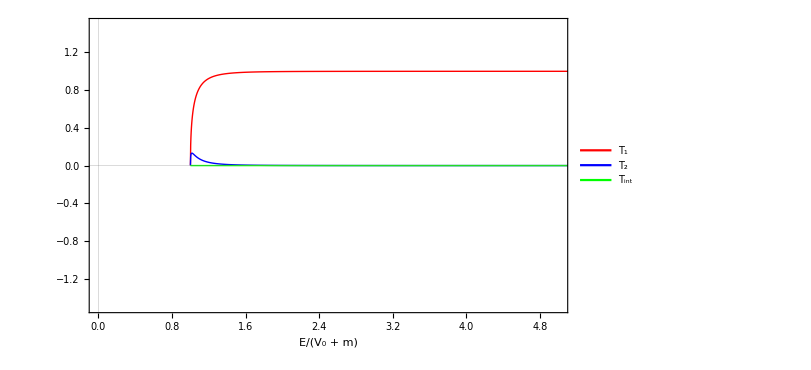

Antisymm-Relativistic-Rep-1-Transmission.jpg

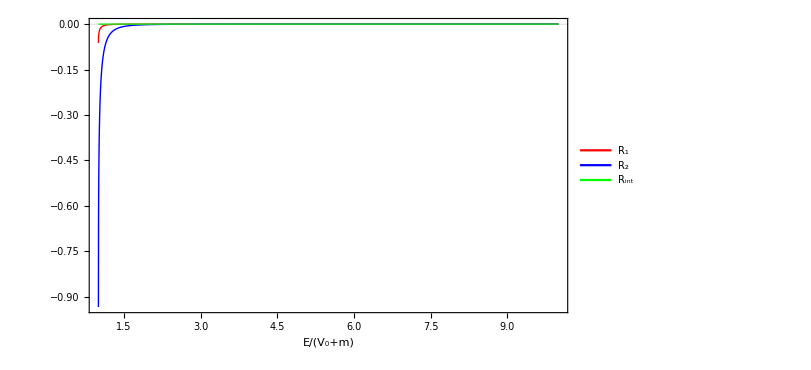

Antisymm-Relativistic-Rep-1-Reflection.jpg

```mathematica
(*Get first symmetric matrix and its c value*)


M1=getAntisymmetricMatrix[19];
c1=getAntisymmetricCValue[19];

Print["\nExample matrix:"];
Print[MatrixForm[M1]];
Print["c value: ",c1];

(*Verify properties*)
Print["Nilpotent (M^2 = 0): ",verifyNilpotent[M1]];
Print["Anticommutator constraint: ",verifyAnticommutator[M1]];

c2= If[c1==4,c1,c1/4*Sqrt[2]]
eta =c2/8*Sqrt[2]  M1


x1 = (eta + ConjugateTranspose[eta])/Sqrt[2];
x2 =  (eta - ConjugateTranspose[eta])/Sqrt[2];

Eigenvalues[ eta  e+  m ConjugateTranspose[eta] ]
Eigenvalues[ x1  e+  m  x2]

Pz =Eigenvectors[  x1  e+  m  x2];

PzA = Pz/. { 1/e^(1/2) ->(Sqrt[2]Sqrt[m])/pz};

PzB = PzA/. { Sqrt[e] Sqrt[m]->pz/Sqrt[2],- Sqrt[e] Sqrt[m]->-pz/Sqrt[2], Sqrt[e^2 - m^2]->pz, Sqrt[e] ->pz/(Sqrt[2]Sqrt[m])
, 1/e^(1/2) ->(Sqrt[2]Sqrt[m])/pz, 1/Sqrt[e^2 - m^2]->1/pz, √(-e^2+m^2)->I pz};

P={{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,0}};

PzD =PzB.P

col[v_]:=List/@v;

u1=col[PzD[[3]]];
u2=col[PzD[[4]]];

u3=col[PzD[[1]]];
u4=col[PzD[[2]]];

Fu1[ee_,ppz_]:=u1/. {e->ee, pz->ppz}
Fu2[ee_,ppz_]:=u2/. {e->ee, pz->ppz}
Fu3[ee_,ppz_]:=u3/. {e->ee, pz->ppz}
Fu4[ee_,ppz_]:=u4/. {e->ee, pz->ppz}

psiIN = a Fu1[e,p1];
psiR = b Fu1[e,-p1] + bp Fu2[e,-p1];
psiT = c  Fu1[e-v0,p2]+ cp Fu2[e-v0,p2];

Xm=x1

sol1 = Solve[a Fu1[e,p1]+b Fu1[e,-p1] + bp Fu2[e,-p1]==c  Fu1[e-v0,p2]+ cp Fu2[e-v0,p2],{a,b,c,bp,cp}]//FullSimplify;

sol2 = sol1/.{p1-> Sqrt[e^2-m^2],p2-> Sqrt[(e-v0)^2-m^2]}//FullSimplify;

jin= ConjugateTranspose[psiIN].Xm.psiIN//FullSimplify;

jT = ConjugateTranspose[psiT].Xm.psiT//FullSimplify;

jR= ConjugateTranspose[psiR].Xm.psiR//FullSimplify;

jTjin =jT/jin/.{p1-> Sqrt[e^2-m^2],p2-> Sqrt[(e-v0)^2-m^2]}//FullSimplify;

jRjin =jR/jin/.{p1-> Sqrt[e^2-m^2],p2-> Sqrt[(e-v0)^2-m^2]}//FullSimplify;

exprT = Expand[jTjin];


Tcc1 =Coefficient[exprT,c*Conjugate[c]] + Coefficient[exprT,Abs[c]^2];
Tcc2 =Tcc1*c*Conjugate[c]/.sol2/.bp->1 ;
Tcc3 [ee_,v00_,mm_,aa_]:=Tcc2/. {e->ee, v0->v00, m->mm,a->aa};

Tcpcp1 =Coefficient[exprT,cp*Conjugate[cp]] + Coefficient[exprT,Abs[cp]^2];
Tcpcp2 =Tcpcp1*cp*Conjugate[cp]/.sol2 /.bp->1;
Tcpcp3 [ee_,v00_,mm_,aa_]:=Tcpcp2/. {e->ee, v0->v00, m->mm,a->aa};

Tcpc1 =Coefficient[exprT,cp*Conjugate[c]];
Tcpc2 =Tcpc1*cp*Conjugate[c]/.sol2/.bp->1 ;
Tcpc3 [ee_,v00_,mm_,aa_]:=Tcpc2/. {e->ee, v0->v00, m->mm,a->aa};

Tccp1 =Coefficient[exprT,c*Conjugate[cp]];
Tccp2 =Tccp1*c*Conjugate[cp]/.sol2/.bp->1 ;
Tccp3 [ee_,v00_,mm_,aa_]:=Tccp2/. {e->ee, v0->v00, m->mm,a->aa};

Ttot [e_,v0_,m_]:=Abs[Tcc3 [e,v0,m,1]+Tcpcp3 [e,v0,m,1]+Tcpc3 [e,v0,m,1]+Tccp3 [e,v0,m,1]];

exprR = Expand[jRjin];
Rbb1 =Coefficient[exprR,b*Conjugate[b]]+Coefficient[exprR,Abs[b]^2];
Rbb2 =Rbb1*b*Conjugate[b]/.sol2/.bp->1 ;
Rbb3 [ee_,v00_,mm_,aa_]:=Rbb2/. {e->ee, v0->v00, m->mm,a->aa};

Rbpbp1 =Coefficient[exprR,bp*Conjugate[bp]] + Coefficient[exprR,Abs[bp]^2];
Rbpbp2 =Rbpbp1*bp*Conjugate[bp]/.sol2/.bp->1 ;
Rbpbp3[ee_,v00_,mm_,aa_]:=Rbpbp2/. {e->ee, v0->v00, m->mm,a->aa};

Rbbp1 =Coefficient[exprR,b*Conjugate[bp]];
Rbbp2 =Rbbp1*b*Conjugate[bp]/.sol2/.bp->1 ;
Rbbp3 [ee_,v00_,mm_,aa_]:=Rbbp2/. {e->ee, v0->v00, m->mm,a->aa};

Rbpb1 =Coefficient[exprR,bp*Conjugate[b]];
Rbpb2 =Rbpb1*bp*Conjugate[b]/.sol2 /.bp->1;
Rbpb3 [ee_,v00_,mm_,aa_]:=Rbpb2/. {e->ee, v0->v00, m->mm,a->aa};

Rtot[e_,v0_,m_]:=Abs[Rbb3 [e,v0,m,1]+Rbpbp3 [e,v0,m,1]+Rbbp3 [e,v0,m,1]+Rbpb3 [e,v0,m,1]];

pout = Plot[{Tcc3[x*(vstep+mev),(vstep+1/2mev),1/2mev,1],Tcpcp3[x*(vstep+mev),(vstep+1/2mev),1/2mev,1],Tccp3[x*(vstep+mev),(vstep+1/2mev),1/2mev,1]},{x,1,10},PlotStyle->{{Red,Thick},{Blue,Thick},{Green,Thick}},Frame->True,FrameLabel->{Style["E/(V:2080 + m)",18,Italic],None},PlotLegends->Placed[{Style["T₁",20,Italic],Style["T₂",20,Italic],Style["T_int",20,Italic]},{0.8,0.3}],ImageSize->{600,600},FrameTicksStyle->Directive[Black,14],PlotRange->{{0,5},{-1.5,1.5}},PlotTheme->"Scientific"]

Export["Antisymm-Relativistic-Rep-1-Transmission.jpg",pout,"JPEG"]

rout = Plot[{Rbb3[x*(vstep+mev),(vstep+1/2mev),1/2mev,1],Rbpbp3[x*(vstep+mev),(vstep+1/2mev),1/2mev,1],Rbbp3[x*(vstep+mev),(vstep+1/2mev),1/2mev,1]},{x,1,10},PlotStyle->{{Red,Thick},{Blue,Thick},{Green,Thick}},Frame->True,FrameLabel->{Style["E/(V₀+m)",18,Italic],None},PlotLegends->Placed[{Style["R₁",18,Italic],Style["R₂",18,Italic],Style["R_int",18,Italic]},{0.8,0.8}],ImageSize->{600,600},FrameTicksStyle->Directive[Black,14],PlotRange->Full,PlotTheme->"Scientific"]

Export["Antisymm-Relativistic-Rep-1-Reflection.jpg",rout,"JPEG"]
```

The transmission coefficients for the three generations

```mathematica
TG1=(e-v0)/e √((e^2-m^2)/(e^2-m^2-2 e v0+v0^2));
TG2=(√((e-m) (e+m) (e-m-v0) (e+m-v0)) (e (√((e-m) (e+m))+√((e-m-v0) (e+m-v0)))-√((e-m) (e+m)) v0)^2)/(e (e-v0) (e^2-m^2+√((e-m) (e+m) (e-m-v0) (e+m-v0))-e v0)^2);


TG3= ((√(e^2-m^2)+√((e-m-v0) (e+m-v0)))^2 (e-v0) √((e-m) (e+m) (e-m-v0) (e+m-v0)))/(e (e^2-m^2+√((e-m) (e+m) (e-m-v0) (e+m-v0))-e v0)^2);
```

```mathematica
TG3/TG2//FullSimplify
```

((√(e^2-m^2)+√((e-m-v0) (e+m-v0)))^2 (e-v0)^2)/(e (√((e-m) (e+m))+√((e-m-v0) (e+m-v0)))-√((e-m) (e+m)) v0)^2

```mathematica
TG3/TG1//FullSimplify
```

((√(e^2-m^2)+√((e-m-v0) (e+m-v0)))^2 (e-m-v0) (e+m-v0))/((e^2-m^2+√((e-m) (e+m) (e-m-v0) (e+m-v0))-e v0)^2)

```mathematica
getAntisymmetricMatrix[16]//MatrixForm
```

(0 | 0 | -ⅈ | -1
0 | 0 | 1 | -ⅈ
ⅈ | -1 | 0 | 0
1 | ⅈ | 0 | 0)

## symmetric matrices

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Adeel\Dropbox\0-Research\NRQM\mathematica\NRQM-Matrx-structure\drafts\so10\A-so10-nilpotent\submission\clean_mathematica

```mathematica
Get["symmetric_matrices.m"];
```

```mathematica
Print["Loaded:"];
Print["  Symmetric matrices: ",countSymmetricMatrices];
```

Loaded:

Symmetric matrices: 432

```mathematica
me=9.1*10^-31;
cv=3*10^8;
ev=me*cv^2/(1.6*10^-19);
mev=me*cv^2/(1.6*10^-19);
jev=(1.6*10^-19);
vstep=mev;

gv = 0.379;
```

Example matrix:

(0 | 0 | 1 | ⅈ
0 | 0 | ⅈ | -1
1 | ⅈ | 0 | 0
ⅈ | -1 | 0 | 0)

c value: 4

Nilpotent (M^2 = 0): True

Anticommutator constraint: True

1/(√2)

{{0,0,1/(√2),ⅈ/(√2)},{0,0,ⅈ/(√2),-1/(√2)},{1/(√2),ⅈ/(√2),0,0},{ⅈ/(√2),-1/(√2),0,0}}

{-√2 √e √m,-√2 √e √m,√2 √e √m,√2 √e √m}

{-√(e^2-m^2),-√(e^2-m^2),√(e^2-m^2),√(e^2-m^2)}

{{1,0,e/pz,-(ⅈ m)/pz},{0,1,-(ⅈ m)/pz,-e/pz},{1,0,-e/pz,(ⅈ m)/pz},{0,1,(ⅈ m)/pz,e/pz}}

{{0,0,1,0},{0,0,0,-1},{1,0,0,0},{0,-1,0,0}}

Solve::svars: Equations may not give solutions for all "solve" variables.

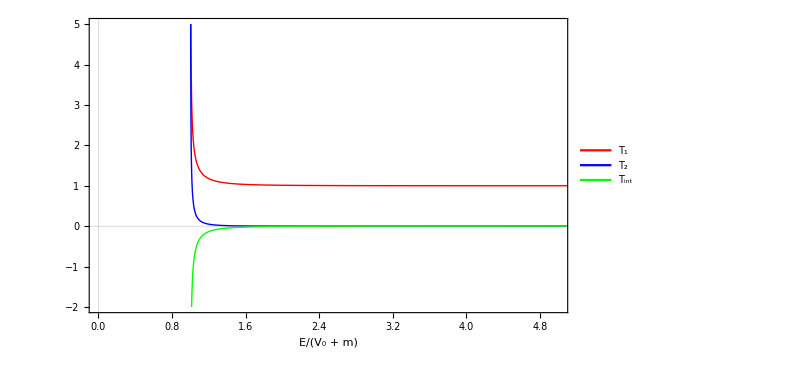

Relativistic-Rep-1-Transmission.jpg

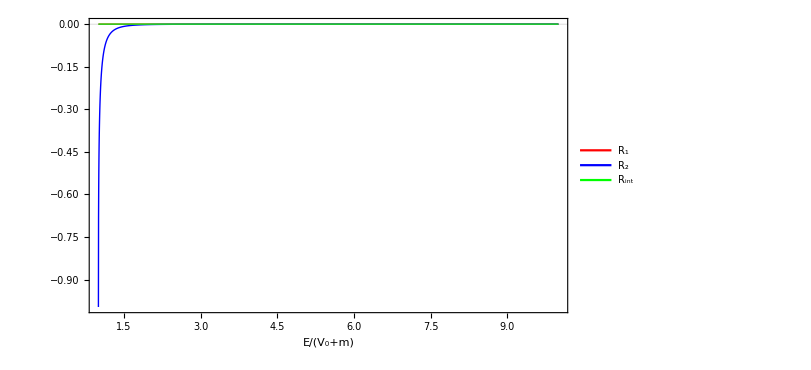

Relativistic-Rep-1-Reflection.jpg

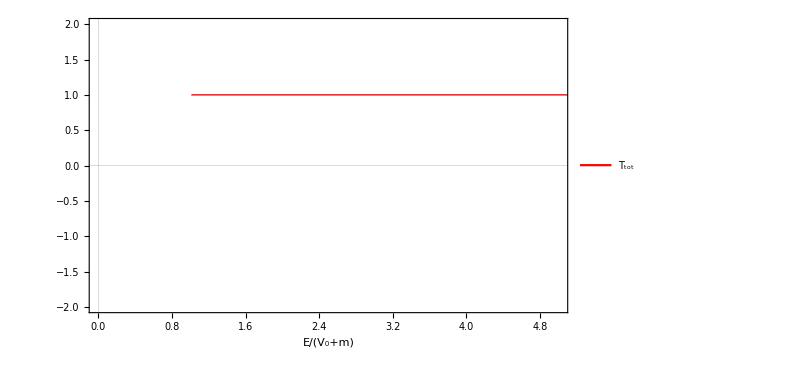

```mathematica
(*Get first symmetric matrix and its c value*)


M1=getSymmetricMatrix[2];
c1=getSymmetricCValue[2];

Print["\nExample matrix:"];
Print[MatrixForm[M1]];
Print["c value: ",c1];

(*Verify properties*)
Print["Nilpotent (M^2 = 0): ",verifyNilpotent[M1]];
Print["Anticommutator constraint: ",verifyAnticommutator[M1]];

c2= If[c1==4,c1/8*Sqrt[2],c1/4*Sqrt[2]]
eta =c2  M1

x1 = (eta + ConjugateTranspose[eta])/Sqrt[2];
x2 =  (eta - ConjugateTranspose[eta])/Sqrt[2];

Eigenvalues[ eta  e+  m ConjugateTranspose[eta] ]
Eigenvalues[ x1  e+  m  x2]

Pz =Eigenvectors[  x1  e+  m  x2];

PzA = Pz/. { 1/e^(1/2) ->(Sqrt[2]Sqrt[m])/pz};

PzB = PzA/. { Sqrt[e] Sqrt[m]->pz/Sqrt[2],- Sqrt[e] Sqrt[m]->-pz/Sqrt[2], Sqrt[e^2 - m^2]->pz, Sqrt[e] ->pz/(Sqrt[2]Sqrt[m])
, 1/e^(1/2) ->(Sqrt[2]Sqrt[m])/pz, 1/Sqrt[e^2 - m^2]->1/pz, √(-e^2+m^2)->I pz};

P={{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,0}};

PzD =PzB.P

col[v_]:=List/@v;

u1=col[PzD[[3]]];
u2=col[PzD[[4]]];

u3=col[PzD[[1]]];
u4=col[PzD[[2]]];

Fu1[ee_,ppz_]:=u1/. {e->ee, pz->ppz}
Fu2[ee_,ppz_]:=u2/. {e->ee, pz->ppz}
Fu3[ee_,ppz_]:=u3/. {e->ee, pz->ppz}
Fu4[ee_,ppz_]:=u4/. {e->ee, pz->ppz}

psiIN = a Fu1[e,p1];
psiR = b Fu1[e,-p1] + bp Fu2[e,-p1];
psiT = c  Fu1[e-v0,p2]+ cp Fu2[e-v0,p2];

Xm=x1

sol1 = Solve[a Fu1[e,p1]+b Fu1[e,-p1] + bp Fu2[e,-p1]==c  Fu1[e-v0,p2]+ cp Fu2[e-v0,p2],{a,b,c,bp,cp}]//FullSimplify;

sol2 = sol1/.{p1-> Sqrt[e^2-m^2],p2-> Sqrt[(e-v0)^2-m^2]}//FullSimplify;

jin= ConjugateTranspose[psiIN].Xm.psiIN//FullSimplify;

jT = ConjugateTranspose[psiT].Xm.psiT//FullSimplify;

jR= ConjugateTranspose[psiR].Xm.psiR//FullSimplify;

jTjin =jT/jin/.{p1-> Sqrt[e^2-m^2]+ϵ,p2-> Sqrt[(e-v0)^2-m^2]+ϵ}//FullSimplify;

jRjin =jR/jin/.{p1-> Sqrt[e^2-m^2]+τ,p2-> Sqrt[(e-v0)^2-m^2]+τ}//FullSimplify;

exprT = Expand[jTjin];


Tcc1 =Coefficient[exprT,c*Conjugate[c]] + Coefficient[exprT,Abs[c]^2];
Tcc2 =Tcc1*c*Conjugate[c]/.sol2/.bp->1 ;
Tcc3 [ee_,v00_,mm_,aa_,ϵϵ_]:=Tcc2/. {e->ee, v0->v00, m->mm,a->aa,ϵ->ϵϵ};

Tcpcp1 =Coefficient[exprT,cp*Conjugate[cp]] + Coefficient[exprT,Abs[cp]^2];
Tcpcp2 =Tcpcp1*cp*Conjugate[cp]/.sol2 /.bp->1;
Tcpcp3 [ee_,v00_,mm_,aa_,ϵϵ_]:=Tcpcp2/. {e->ee, v0->v00, m->mm,a->aa,ϵ->ϵϵ};

Tcpc1 =Coefficient[exprT,cp*Conjugate[c]];
Tcpc2 =Tcpc1*cp*Conjugate[c]/.sol2/.bp->1 ;
Tcpc3 [ee_,v00_,mm_,aa_,ϵϵ_]:=Tcpc2/. {e->ee, v0->v00, m->mm,a->aa,ϵ->ϵϵ};

Tccp1 =Coefficient[exprT,c*Conjugate[cp]];
Tccp2 =Tccp1*c*Conjugate[cp]/.sol2/.bp->1 ;
Tccp3 [ee_,v00_,mm_,aa_,ϵϵ_]:=Tccp2/. {e->ee, v0->v00, m->mm,a->aa,ϵ->ϵϵ};

Ttot [e_,v0_,m_]:=Abs[Tcc3 [e,v0,m,1,0.000001]+Tcpcp3 [e,v0,m,1,0.000001]+Tcpc3 [e,v0,m,1,0.000001]+Tccp3 [e,v0,m,1,0.000001]];

exprR = Expand[jRjin];
Rbb1 =Coefficient[exprR,b*Conjugate[b]]+Coefficient[exprR,Abs[b]^2];
Rbb2 =Rbb1*b*Conjugate[b]/.sol2/.bp->1 ;
Rbb3 [ee_,v00_,mm_,aa_,ττ_]:=Rbb2/. {e->ee, v0->v00, m->mm,a->aa,τ->ττ};

Rbpbp1 =Coefficient[exprR,bp*Conjugate[bp]] + Coefficient[exprR,Abs[bp]^2];
Rbpbp2 =Rbpbp1*bp*Conjugate[bp]/.sol2/.bp->1 ;
Rbpbp3[ee_,v00_,mm_,aa_,ττ_]:=Rbpbp2/. {e->ee, v0->v00, m->mm,a->aa,τ->ττ};

Rbbp1 =Coefficient[exprR,b*Conjugate[bp]];
Rbbp2 =Rbbp1*b*Conjugate[bp]/.sol2/.bp->1 ;
Rbbp3 [ee_,v00_,mm_,aa_,ττ_]:=Rbbp2/. {e->ee, v0->v00, m->mm,a->aa,τ->ττ};

Rbpb1 =Coefficient[exprR,bp*Conjugate[b]];
Rbpb2 =Rbpb1*bp*Conjugate[b]/.sol2 /.bp->1;
Rbpb3 [ee_,v00_,mm_,aa_,ττ_]:=Rbpb2/. {e->ee, v0->v00, m->mm,a->aa,τ->ττ};

Rtot[e_,v0_,m_]:=Abs[Rbb3 [e,v0,m,1,0.0001]+Rbpbp3 [e,v0,m,1,0.0001]+Rbbp3 [e,v0,m,1,0.0001]+Rbpb3 [e,v0,m,1,0.0001]];

pout = Plot[{FullSimplify[Tcc3[x*(vstep+mev),(vstep+1/2mev),1/2mev,1,0.0001]],
FullSimplify[Tcpcp3[x*(vstep+mev),(vstep+1/2mev),1/2mev,1,0.0001]],
FullSimplify[Tccp3[x*(vstep+mev),(vstep+1/2mev),1/2mev,1,0.0001]]},{x,1,10},PlotStyle->{{Red,Thick},{Blue,Thick},{Green,Thick}},Frame->True,FrameLabel->{Style["E/(V:2080 + m)",18,Italic],None,Style["c = "<>ToString[c1]<>" ",22,Italic]},PlotLegends->Placed[{Style["T₁",18,Italic],Style["T₂",18,Italic],Style["T_int",18,Italic]},{0.8,0.8}],ImageSize->{600,600},FrameTicksStyle->Directive[Black,14],PlotRange->{{0,5},{-2,5}},PlotTheme->"Scientific"]

Export["Relativistic-Rep-1-Transmission.jpg",pout,"JPEG"]

rout = Plot[{FullSimplify[Rbb3[x*(vstep+mev),(vstep+1/2mev),1/2mev,1,0.0001]],
FullSimplify[Rbpbp3[x*(vstep+mev),(vstep+1/2mev),1/2mev,1,0.0001]],
FullSimplify[Rbbp3[x*(vstep+mev),(vstep+1/2mev),1/2mev,1,0.0001]]},{x,1,10},PlotStyle->{{Red,Thick},{Blue,Thick},{Green,Thick}},Frame->True,FrameLabel->{Style["E/(V₀+m)",18,Italic],None},PlotLegends->Placed[{Style["R₁",18,Italic],Style["R₂",18,Italic],Style["R_int",18,Italic]},{0.8,0.8}],ImageSize->{600,600},FrameTicksStyle->Directive[Black,14],PlotRange->Full,PlotTheme->"Scientific"]

Export["Relativistic-Rep-1-Reflection.jpg",rout,"JPEG"]

Ttotal[x_]:= Abs[Tcc3[x*(vstep+mev),(vstep+1/2mev),1/2mev,1,0.0001]+
Tcpcp3[x*(vstep+mev),(vstep+1/2mev),1/2mev,1,0.0001]+
Tccp3[x*(vstep+mev),(vstep+1/2mev),1/2mev,1,0.0001]+
Tcpc3[x*(vstep+mev),(vstep+1/2mev),1/2mev,1,0.0001]]+
Abs[Rbb3[x*(vstep+mev),(vstep+1/2mev),1/2mev,1,0.0001]+
Rbpbp3[x*(vstep+mev),(vstep+1/2mev),1/2mev,1,0.0001]+
Rbbp3[x*(vstep+mev),(vstep+1/2mev),1/2mev,1,0.0001]+
Rbpb3[x*(vstep+mev),(vstep+1/2mev),1/2mev,1,0.0001]]

Ttotal2[x_]:=Ttot [x,2,1] + Rtot [x,2,1]

Tout = Plot[{FullSimplify[Ttotal[x]]},{x,1.01,10},PlotStyle->{{Red,Thick},{Blue,Thick},{Green,Thick}},Frame->True,FrameLabel->{Style["E/(V₀+m)",18,Italic],None},PlotLegends->Placed[{Style["T_tot",18,Italic],Style["R₂",18,Italic],Style["R_int",18,Italic]},{0.8,0.8}],ImageSize->{600,600},FrameTicksStyle->Directive[Black,14],PlotRange->{{0,5},{-2,2}},PlotTheme->"Scientific"]
```

```mathematica
hm=Inverse[x1].(I4 pz + x2 m)
```

{{0,0,-ⅈ m+pz,0},{0,pz,0,ⅈ m},{ⅈ m+pz,0,0,0},{0,-ⅈ m,0,-pz}}

```mathematica
herm[hm]//FullSimplify
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
(*Get first symmetric matrix and its c value*)

For[i=1,i<=432,i++,
(M1=getSymmetricMatrix[i];
c1=getSymmetricCValue[i];

Print["\nExample matrix:"];
Print[MatrixForm[M1]];
Print["c value: ",c1];

(*Verify properties*)
Print["Nilpotent (M^2 = 0): ",verifyNilpotent[M1]];
     Print["Anticommutator constraint: ",verifyAnticommutator[M1]];

 c2= If[c1==4,c1/8*Sqrt[2],c1/4*Sqrt[2]];

eta =c2  M1;


      x1 = (eta + ConjugateTranspose[eta])/Sqrt[2];
x2 =  (eta - ConjugateTranspose[eta])/Sqrt[2];

Ev1=Eigenvalues[ eta  e+  m ConjugateTranspose[eta] ];
Ev2=Eigenvalues[ x1  e+  m  x2];

Pz =Eigenvectors[  x1  e+  m  x2];

Print[Ev2];

PzA = Pz/. { 1/e^(1/2) ->(Sqrt[2]Sqrt[m])/pz};

PzB = PzA/. { Sqrt[e] Sqrt[m]->pz/Sqrt[2],- Sqrt[e] Sqrt[m]->-pz/Sqrt[2], Sqrt[e^2 - m^2]->pz, Sqrt[e] ->pz/(Sqrt[2]Sqrt[m])
, 1/e^(1/2) ->(Sqrt[2]Sqrt[m])/pz, 1/Sqrt[e^2 - m^2]->1/pz, √(-e^2+m^2)->I pz};

P={{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,0}};

PzD =PzB.P;

col[v_]:=List/@v;

u1=col[PzD[[3]]];
u2=col[PzD[[4]]];

u3=col[PzD[[1]]];
u4=col[PzD[[2]]];

Fu1[ee_,ppz_]:=u1/. {e->ee, pz->ppz};
Fu2[ee_,ppz_]:=u2/. {e->ee, pz->ppz};
Fu3[ee_,ppz_]:=u3/. {e->ee, pz->ppz};
Fu4[ee_,ppz_]:=u4/. {e->ee, pz->ppz};

psiIN = a Fu1[e,p1];
psiR = b Fu1[e,-p1] + bp Fu2[e,-p1];
psiT = c  Fu1[e-v0,p2]+ cp Fu2[e-v0,p2];

Xm=x1;

sol1 = Solve[a Fu1[e,p1]+b Fu1[e,-p1] + bp Fu2[e,-p1]==c  Fu1[e-v0,p2]+ cp Fu2[e-v0,p2],{a,b,c,bp,cp}]//FullSimplify;

sol2 = sol1/.{p1-> Sqrt[e^2-m^2],p2-> Sqrt[(e-v0)^2-m^2]}//FullSimplify;

jin= ConjugateTranspose[psiIN].Xm.psiIN//FullSimplify;

jT = ConjugateTranspose[psiT].Xm.psiT//FullSimplify;

jR= ConjugateTranspose[psiR].Xm.psiR//FullSimplify;

jTjin =jT/jin/.{p1-> Sqrt[e^2-m^2]+ϵ,p2-> Sqrt[(e-v0)^2-m^2]+ϵ}//FullSimplify;

jRjin =jR/jin/.{p1-> Sqrt[e^2-m^2]+τ,p2-> Sqrt[(e-v0)^2-m^2]+τ}//FullSimplify;

exprT = Expand[jTjin];


Tcc1 =Coefficient[exprT,c*Conjugate[c]] + Coefficient[exprT,Abs[c]^2];
Tcc2 =Tcc1*c*Conjugate[c]/.sol2/.bp->1 ;
Tcc3 [ee_,v00_,mm_,aa_,ϵϵ_]:=Tcc2/. {e->ee, v0->v00, m->mm,a->aa,ϵ->ϵϵ};

Tcpcp1 =Coefficient[exprT,cp*Conjugate[cp]] + Coefficient[exprT,Abs[cp]^2];
Tcpcp2 =Tcpcp1*cp*Conjugate[cp]/.sol2 /.bp->1;
Tcpcp3 [ee_,v00_,mm_,aa_,ϵϵ_]:=Tcpcp2/. {e->ee, v0->v00, m->mm,a->aa,ϵ->ϵϵ};

Tcpc1 =Coefficient[exprT,cp*Conjugate[c]];
Tcpc2 =Tcpc1*cp*Conjugate[c]/.sol2/.bp->1 ;
Tcpc3 [ee_,v00_,mm_,aa_,ϵϵ_]:=Tcpc2/. {e->ee, v0->v00, m->mm,a->aa,ϵ->ϵϵ};

Tccp1 =Coefficient[exprT,c*Conjugate[cp]];
Tccp2 =Tccp1*c*Conjugate[cp]/.sol2/.bp->1 ;
Tccp3 [ee_,v00_,mm_,aa_,ϵϵ_]:=Tccp2/. {e->ee, v0->v00, m->mm,a->aa,ϵ->ϵϵ};

Ttot [e_,v0_,m_]:=Abs[Tcc3 [e,v0,m,1,0.000001]+Tcpcp3 [e,v0,m,1,0.000001]+Tcpc3 [e,v0,m,1,0.000001]+Tccp3 [e,v0,m,1,0.000001]];

exprR = Expand[jRjin];
Rbb1 =Coefficient[exprR,b*Conjugate[b]]+Coefficient[exprR,Abs[b]^2];
Rbb2 =Rbb1*b*Conjugate[b]/.sol2/.bp->1 ;
Rbb3 [ee_,v00_,mm_,aa_,ττ_]:=Rbb2/. {e->ee, v0->v00, m->mm,a->aa,τ->ττ};

Rbpbp1 =Coefficient[exprR,bp*Conjugate[bp]] + Coefficient[exprR,Abs[bp]^2];
Rbpbp2 =Rbpbp1*bp*Conjugate[bp]/.sol2/.bp->1 ;
Rbpbp3[ee_,v00_,mm_,aa_,ττ_]:=Rbpbp2/. {e->ee, v0->v00, m->mm,a->aa,τ->ττ};

Rbbp1 =Coefficient[exprR,b*Conjugate[bp]];
Rbbp2 =Rbbp1*b*Conjugate[bp]/.sol2/.bp->1 ;
Rbbp3 [ee_,v00_,mm_,aa_,ττ_]:=Rbbp2/. {e->ee, v0->v00, m->mm,a->aa,τ->ττ};

Rbpb1 =Coefficient[exprR,bp*Conjugate[b]];
Rbpb2 =Rbpb1*bp*Conjugate[b]/.sol2 /.bp->1;
Rbpb3 [ee_,v00_,mm_,aa_,ττ_]:=Rbpb2/. {e->ee, v0->v00, m->mm,a->aa,τ->ττ};

Rtot[e_,v0_,m_]:=Abs[Rbb3 [e,v0,m,1,0.0001]+Rbpbp3 [e,v0,m,1,0.0001]+Rbbp3 [e,v0,m,1,0.0001]+Rbpb3 [e,v0,m,1,0.0001]];

pout = Plot[{FullSimplify[Tcc3[x*(vstep+mev),(vstep+1/2mev),1/2mev,1,0.0001]],
FullSimplify[Tcpcp3[x*(vstep+mev),(vstep+1/2mev),1/2mev,1,0.0001]],
FullSimplify[Tccp3[x*(vstep+mev),(vstep+1/2mev),1/2mev,1,0.0001]]},{x,1,10},PlotStyle->{{Red,Thick},{Blue,Thick},{Green,Thick}},Frame->True,FrameLabel->{Style["E/(V:2080 + m)",18,Italic],None,Style["c = "<>ToString[c1]<>" ",22,Italic]},PlotLegends->Placed[{Style["T₁",18,Italic],Style["T₂",18,Italic],Style["T_int",18,Italic]},{0.8,0.8}],ImageSize->{600,600},FrameTicksStyle->Directive[Black,14],PlotRange->{{0,5},{-2,2}},PlotTheme->"Scientific"];

Export["Relativistic-symmetric/Relativistic-transmission-symmetric/Relativistic-Rep-Transmission-"<>ToString[i]<>".jpg",pout,"JPEG"];

rout = Plot[{FullSimplify[Rbb3[x*(vstep+mev),(vstep+1/2mev),1/2mev,1,0.0001]],
FullSimplify[Rbpbp3[x*(vstep+mev),(vstep+1/2mev),1/2mev,1,0.0001]],
FullSimplify[Rbbp3[x*(vstep+mev),(vstep+1/2mev),1/2mev,1,0.0001]]},{x,1,10},PlotStyle->{{Red,Thick},{Blue,Thick},{Green,Thick}},Frame->True,FrameLabel->{Style["E/(V₀+m)",18,Italic],None},PlotLegends->Placed[{Style["R₁",18,Italic],Style["R₂",18,Italic],Style["R_int",18,Italic]},{0.8,0.8}],ImageSize->{600,600},FrameTicksStyle->Directive[Black,14],PlotRange->Full,PlotTheme->"Scientific"];

Export["Relativistic-symmetric/Relativistic-reflection-symmetric/Relativistic-Rep-Reflection-"<>ToString[i]<>".jpg",rout,"JPEG"];

Ttotal[x_]:= Abs[Tcc3[x*(vstep+mev),(vstep+1/2mev),1/2mev,1,0.0001]+
Tcpcp3[x*(vstep+mev),(vstep+1/2mev),1/2mev,1,0.0001]+
Tccp3[x*(vstep+mev),(vstep+1/2mev),1/2mev,1,0.0001]+
Tcpc3[x*(vstep+mev),(vstep+1/2mev),1/2mev,1,0.0001]]+
Abs[Rbb3[x*(vstep+mev),(vstep+1/2mev),1/2mev,1,0.0001]+
Rbpbp3[x*(vstep+mev),(vstep+1/2mev),1/2mev,1,0.0001]+
Rbbp3[x*(vstep+mev),(vstep+1/2mev),1/2mev,1,0.0001]+
Rbpb3[x*(vstep+mev),(vstep+1/2mev),1/2mev,1,0.0001]];

Ttotal2[x_]:=Ttot [x,2,1] + Rtot [x,2,1];

Tout = Plot[{FullSimplify[Ttotal[x]]},{x,1.01,10},PlotStyle->{{Red,Thick},{Blue,Thick},{Green,Thick}},Frame->True,FrameLabel->{Style["E/(V₀+m)",18,Italic],None},PlotLegends->Placed[{Style["T_tot",18,Italic],Style["R₂",18,Italic],Style["R_int",18,Italic]},{0.8,0.8}],ImageSize->{600,600},FrameTicksStyle->Directive[Black,14],PlotRange->{{0,5},{-2,2}},PlotTheme->"Scientific"];
Export["Relativistic-symmetric/Relativistic-total-symmetric/Relativistic-Rep-Total-"<>ToString[i]<>".jpg",Tout,"JPEG"];)]
```

Example matrix:

(0 | 0 | 1 | ⅈ
0 | 0 | ⅈ | -1
1 | ⅈ | 0 | 0
ⅈ | -1 | 0 | 0)

c value: 4

Nilpotent (M^2 = 0): True

Anticommutator constraint: True

{-√(e^2-m^2),-√(e^2-m^2),√(e^2-m^2),√(e^2-m^2)}

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
getSymmetricMatrix[2]//MatrixForm  (*diverging with spin flip and interference*)
```

(0 | 0 | 1 | ⅈ
0 | 0 | ⅈ | -1
1 | ⅈ | 0 | 0
ⅈ | -1 | 0 | 0)